Лабораторная работа №1
Численное решение задачи Коши для системы дифференциальных уравнений методом Эйлера и его модификацией

-Graphics-

Метод Эйлера с шагом h:

```mathematica
f1[t_,x1_,x2_]:=t^2*x1+x2;
g1[t_,x1_,x2_]:=Cos[x1+t*x2];
h=0.1;
a=0;
b=2;
t=a;
n=(b-a)/h;
x1=-1;
x2=1;
tx1={{t,x1}};
tx2={{t,x2}};
tx1x2={{t,x1,x2}};
For[i=0,i<n,i++,
f1n=f1[t,x1,x2];
g1n=g1[t,x1,x2];
x1=x1+h*f1n;
x2=x2+h*g1n;
t=t+h;
tx1x2=Append[tx1x2,{t,x1,x2}];
tx1=Append[tx1,{t,x1}];
tx2=Append[tx2,{t,x2}]];
```

Модифицированный метод Эйлера с шагом h:

```mathematica
f2[t_,x1_,x2_]:=t^2*x1+x2;
g2[t_,x1_,x2_]:=Cos[x1+t*x2];
t=a;
n=(b-a)/h;
x1=-1;
x2=1;
t2x1x2={{t2,x1,x2}};
t2x1={{t,x1}};
t2x2={{t,x2}};
```

```mathematica
For[i=0,i<n,i++,
f2n=f2[t,x1,x2];
g2n=g2[t,x1,x2];
x11=x1+h*f2n;
x22=x2+h*g2n;
fn2=f2[t+h,x11,x22];
gn2=g2[t+h,x11,x22];
x1=x1+h*(f2n+fn2)/2;
x2=x2+h*(g2n+gn2)/2;
t=t+h;
t2x1=Append[t2x1,{t,x1}];
t2x2=Append[t2x2,{t,x2}];
t2x1x2=Append[t2x1x2,{t,x1,x2}]];
```

Точное решение :

```mathematica
{sol1,sol2}=NDSolveValue[{y'[t1]==(t1^2)*y[t1]+z[t1],z'[t1]==Cos[y[t1]+t1*z[t1]],y[0]==-1,z[0]==1},{y,z},{t1,0,2}]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
sol={};
m=0;
For[k=0,k<21,k++,
AppendTo[sol,{m,sol1[m],sol2[m]}];
m=m+h]
TableForm[sol];
```

```mathematica
s=Table[{tx1x2[[j,1]],tx1x2[[j,2]],tx1x2[[j,3]],t2x1x2[[j,2]],t2x1x2[[j,3]],sol[[j,2]],sol[[j,3]]},{j,21}];
Grid[Join[{{"t","x1, метод Эйлера","x2, метод Эйлера","x1, мод метод Эйлера","x2, мод метод Эйлера","x1, точное решение","x2, точное решение"}},s],Frame->All]
```

t | x1, метод Эйлера | x2, метод Эйлера | x1, мод метод Эйлера | x2, мод метод Эйлера | x1, точное решение | x2, точное решение
0 | -1 | 1 | -1 | 1 | -1. | 1.
0.1 | -0.9 | 1.05403 | -0.897748 | 1.06204 | -0.89733 | 1.06227
0.2 | -0.795497 | 1.12409 | -0.790064 | 1.13938 | -0.789279 | 1.13998
0.3 | -0.68627 | 1.20824 | -0.676532 | 1.22927 | -0.675445 | 1.23038
0.4 | -0.571623 | 1.30304 | -0.556362 | 1.3269 | -0.555057 | 1.32865
0.5 | -0.450464 | 1.40292 | -0.428531 | 1.42493 | -0.427124 | 1.42742
0.6 | -0.321434 | 1.49978 | -0.291937 | 1.51374 | -0.290565 | 1.51698
0.7 | -0.183027 | 1.58352 | -0.145439 | 1.58298 | -0.14425 | 1.58684
0.8 | -0.033644 | 1.64366 | 0.0123366 | 1.62407 | 0.0132183 | 1.62826
0.9 | 0.128569 | 1.67221 | 0.183529 | 1.63241 | 0.184027 | 1.63655
1. | 0.306205 | 1.66594 | 0.371876 | 1.60816 | 0.371971 | 1.61184
1.1 | 0.503419 | 1.62687 | 0.583774 | 1.55514 | 0.583508 | 1.55804
1.2 | 0.72702 | 1.56077 | 0.829609 | 1.47927 | 0.829121 | 1.48121
1.3 | 0.987788 | 1.47509 | 1.12567 | 1.38766 | 1.1253 | 1.38858
1.4 | 1.30223 | 1.37786 | 1.49722 | 1.28913 | 1.49775 | 1.28921
1.5 | 1.69526 | 1.27826 | 1.98388 | 1.19751 | 1.98709 | 1.19755
1.6 | 2.20452 | 1.18915 | 2.64921 | 1.13905 | 2.65908 | 1.14197
1.7 | 2.88779 | 1.13226 | 3.59829 | 1.15638 | 3.62356 | 1.16909
1.8 | 3.83558 | 1.14227 | 5.00776 | 1.23264 | 5.06465 | 1.2564
1.9 | 5.19254 | 1.2347 | 7.16423 | 1.21318 | 7.28181 | 1.21492
2. | 7.19052 | 1.26573 | 10.5481 | 1.20785 | 10.798 | 1.22456

Графики x1(t), x2(t)  для метода Эйлера, сопоставленные с графиками точного решения:

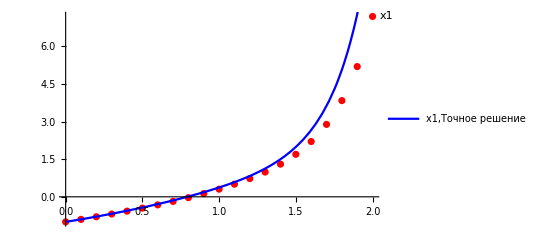

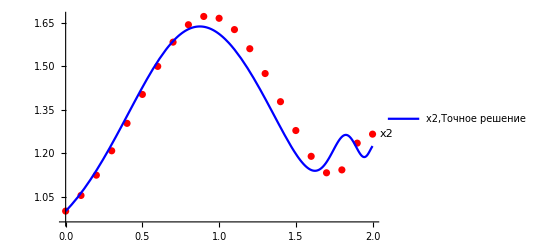

```mathematica
Show[ListPlot[Labeled[tx1,"x1"],PlotStyle->Red],Plot[sol1[t],{t,0,2},PlotLegends->{Placed[{Text[Style["x1,Точное решение",12]]},{0.5,0.7}]},PlotStyle->Blue]]
Show[ListPlot[Labeled[tx2,"x2"],PlotStyle->Red],Plot[sol2[t],{t,0,2},PlotLegends->{Placed[{Text[Style["x2,Точное решение",12]]},{0.5,0.7}]},PlotStyle->Blue]]
```

Графики x1 (t), x2 (t)  для модифицированного метода Эйлера, сопоставленные с графиками точного решения :

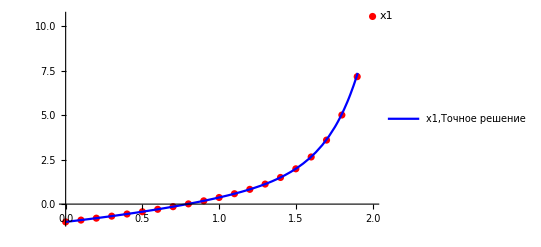

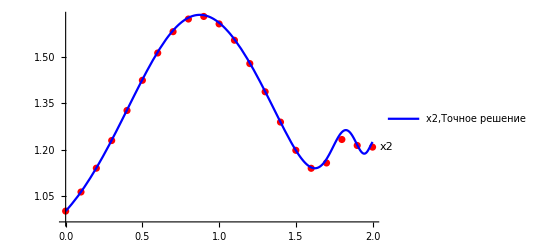

```mathematica
Show[ListPlot[Labeled[t2x1,"x1"],PlotStyle->Red],Plot[sol1[t],{t,0,2},PlotLegends->{Placed[{Text[Style["x1,Точное решение",12]]},{0.5,0.7}]},PlotStyle->Blue]]
Show[ListPlot[Labeled[t2x2,"x2"],PlotStyle->Red],Plot[sol2[t],{t,0,2},PlotLegends->{Placed[{Text[Style["x2,Точное решение",12]]},{0.6,0.7}]},PlotStyle->Blue]]
```

Графики фазовых траекторий:

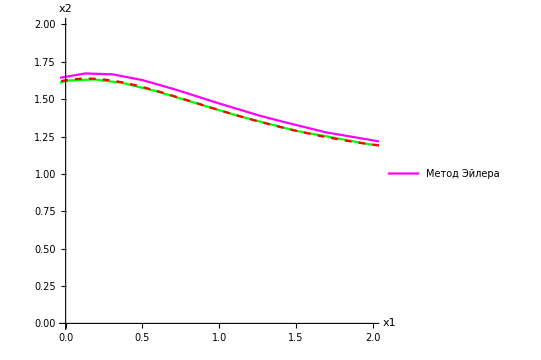

```mathematica
{sol11,sol22}={Interpolation[tx1,InterpolationOrder->1],Interpolation[tx2,InterpolationOrder->1]};
{sol111,sol222}={Interpolation[t2x1,InterpolationOrder->1],Interpolation[t2x2,InterpolationOrder->1]};
Show[ParametricPlot[{sol11[t],sol22[t]},{t,0,2},AxesLabel->{"x1","x2"},PlotRange->{0,2},PlotStyle->Magenta,PlotLegends->{Placed[{Text[Style["Метод Эйлера",12]]},{0.6,0.9}]},AspectRatio->0.9],ParametricPlot[{sol111[t],sol222[t]},{t,0,2},AxesLabel->{"x1","x2"},PlotRange->{0,2},PlotStyle->Green,PlotLegends->{Placed[{Text[Style["Модифицированный метод Эйлера",12]]},{0.7,0.7}]},AspectRatio->0.9],ParametricPlot[{sol1[t],sol2[t]},{t,0,2},AxesLabel->{"x1","x2"},AspectRatio->0.9,PlotStyle->{Red,Dashed},PlotLegends->{Placed[{Text[Style["Точное решение",12]]},{0.7,0.7}]}]]
```

Метод Эйлера  шагом 2h:

```mathematica
f1[t_,x1_,x2_]:=t^2*x1+x2;
g1[t_,x1_,x2_]:=Cos[x1+t*x2];
h2=2*h;
a=0;
b=2;
t3=a;
n2=(b-a)/h2;
x1=-1;
x2=1;
t3x1={{t3,x1}};
t3x2={{t3,x2}};
t3x1x2={{t3,x1,x2}};
For[i=0,i<n2,i++,
f2n=f1[t3,x1,x2];
g2n=g1[t3,x1,x2];
x1=x1+h2*f2n;
x2=x2+h2*g2n;
t3=t3+h2;
t3x1x2=Append[t3x1x2,{t3,x1,x2}];
t3x1=Append[t3x1,{t3,x1}];
t3x2=Append[t3x2,{t3,x2}]];
```

Модифицированный метод Эйлера с шагом 2h:

```mathematica
a=0;
b=2;
t4=a;
x1=-1;
x2=1;
t4x1x2={{t4,x1,x2}};
t4x1={{t4,x1}};
t4x2={{t4,x2}};
```

```mathematica
For[i=0,i<n2,i++,
f4n=f2[t4,x1,x2];
g4n=g2[t4,x1,x2];
x11=x1+h2*f4n;
x22=x2+h2*g4n;
fn4=f2[t4+h2,x11,x22];
gn4=g2[t4+h2,x11,x22];
x1=x1+h2*(f4n+fn4)/2;
x2=x2+h2*(g4n+gn4)/2;
t4=t4+h2;
t4x1=Append[t4x1,{t4,x1}];
t4x2=Append[t4x2,{t4,x2}];
t4x1x2=Append[t4x1x2,{t4,x1,x2}]];
```

Погрешность для метода Эйлера:

```mathematica
pogr1={};
pogr2={};
Pogresh1=0;
For[i=1,i≤n2+1,i++,
t5x1=Abs[tx1[[2i-1,2]]-t3x1[[i,2]]];
t5x2=Abs[tx2[[2i-1,2]]-t3x2[[i,2]]];
PogreshTest=Sqrt[t5x1^2+t5x2^2];
If[PogreshTest>Pogresh1,Pogresh1=PogreshTest]];
Pogresh1
```

1.86203

Погрешность для модифицированного метода Эйлера:

```mathematica
n3=(b-a)/h2;
pogr3={};
pogr4={};
Pogresh2=0;
For[i=1,i≤n3+1,i++,
t6x1=(Abs[t2x1[[2i-1,2]]-t4x1[[i,2]]]);
t6x2=(Abs[t2x2[[2i-1,2]]-t4x2[[i,2]]]);
PogreshTest=Sqrt[t6x1^2+t6x2^2];
If[PogreshTest>Pogresh2,Pogresh2=PogreshTest]
];
Pogresh2/3
```

0.177963